## Doing Fewer Computations

L = 5

nParticles = 5

J Matrix:

(0 | J01 | J02 | J03 | J04 | J05
J01 | 0 | J12 | J13 | J14 | J15
J02 | J12 | 0 | J23 | J24 | J25
J03 | J13 | J23 | 0 | J34 | J35
J04 | J14 | J24 | J34 | 0 | J45
J05 | J15 | J25 | J35 | J45 | 0)

Total configurations: 120

First few: {{1,2,3,4,5},{1,2,3,5,4},{1,2,4,3,5},{1,2,4,5,3},{1,2,5,3,4}}

Transition matrix row sums: {1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Transition matrix:

Showing 5x5 block:

(1/4 (1-(Piecewise[{{1, -J13+J15+J23-J25≤0}, {ⅇ^(-((-J13+J15+J23-J25) β)), -J13+J15+J23-J25>0}, {0, True}}]))+1/4 (1-(Piecewise[{{1, J12-J13-J24+J34≤0}, {ⅇ^(-((J12-J13-J24+J34) β)), J12-J13-J24+J34>0}, {0, True}}]))+1/8 (1-(Piecewise[{{1, -J14+J15+J34-J35≤0}, {ⅇ^(-((-J14+J15+J34-J35) β)), -J14+J15+J34-J35>0}, {0, True}}]))+1/8 (1-(Piecewise[{{1, J12-J14-J25+J45≤0}, {ⅇ^(-((J12-J14-J25+J45) β)), J12-J14-J25+J45>0}, {0, True}}]))+1/4 (1-(Piecewise[{{1, J23-J24-J35+J45≤0}, {ⅇ^(-((J23-J24-J35+J45) β)), J23-J24-J35+J45>0}, {0, True}}])) | 1/8 (Piecewise[{{1, -J14+J15+J34-J35≤0}, {ⅇ^(-((-J14+J15+J34-J35) β)), -J14+J15+J34-J35>0}, {0, True}}]) | 1/4 (Piecewise[{{1, J23-J24-J35+J45≤0}, {ⅇ^(-((J23-J24-J35+J45) β)), J23-J24-J35+J45>0}, {0, True}}]) | 0 | 0
1/8 (Piecewise[{{1, J14-J15-J34+J35≤0}, {ⅇ^(-((J14-J15-J34+J35) β)), J14-J15-J34+J35>0}, {0, True}}]) | 1/4 (1-(Piecewise[{{1, -J13+J14+J23-J24≤0}, {ⅇ^(-((-J13+J14+J23-J24) β)), -J13+J14+J23-J24>0}, {0, True}}]))+1/4 (1-(Piecewise[{{1, J12-J13-J25+J35≤0}, {ⅇ^(-((J12-J13-J25+J35) β)), J12-J13-J25+J35>0}, {0, True}}]))+1/8 (1-(Piecewise[{{1, J14-J15-J34+J35≤0}, {ⅇ^(-((J14-J15-J34+J35) β)), J14-J15-J34+J35>0}, {0, True}}]))+1/8 (1-(Piecewise[{{1, J12-J15-J24+J45≤0}, {ⅇ^(-((J12-J15-J24+J45) β)), J12-J15-J24+J45>0}, {0, True}}]))+1/4 (1-(Piecewise[{{1, J23-J25-J34+J45≤0}, {ⅇ^(-((J23-J25-J34+J45) β)), J23-J25-J34+J45>0}, {0, True}}])) | 0 | 0 | 1/4 (Piecewise[{{1, J23-J25-J34+J45≤0}, {ⅇ^(-((J23-J25-J34+J45) β)), J23-J25-J34+J45>0}, {0, True}}])
1/4 (Piecewise[{{1, -J23+J24+J35-J45≤0}, {ⅇ^(-((-J23+J24+J35-J45) β)), -J23+J24+J35-J45>0}, {0, True}}]) | 0 | 1/4 (1-(Piecewise[{{1, -J14+J15+J24-J25≤0}, {ⅇ^(-((-J14+J15+J24-J25) β)), -J14+J15+J24-J25>0}, {0, True}}]))+1/4 (1-(Piecewise[{{1, J12-J14-J23+J34≤0}, {ⅇ^(-((J12-J14-J23+J34) β)), J12-J14-J23+J34>0}, {0, True}}]))+1/8 (1-(Piecewise[{{1, J12-J13-J25+J35≤0}, {ⅇ^(-((J12-J13-J25+J35) β)), J12-J13-J25+J35>0}, {0, True}}]))+1/8 (1-(Piecewise[{{1, -J13+J15+J34-J45≤0}, {ⅇ^(-((-J13+J15+J34-J45) β)), -J13+J15+J34-J45>0}, {0, True}}]))+1/4 (1-(Piecewise[{{1, -J23+J24+J35-J45≤0}, {ⅇ^(-((-J23+J24+J35-J45) β)), -J23+J24+J35-J45>0}, {0, True}}])) | 1/8 (Piecewise[{{1, -J13+J15+J34-J45≤0}, {ⅇ^(-((-J13+J15+J34-J45) β)), -J13+J15+J34-J45>0}, {0, True}}]) | 0
0 | 0 | 1/8 (Piecewise[{{1, J13-J15-J34+J45≤0}, {ⅇ^(-((J13-J15-J34+J45) β)), J13-J15-J34+J45>0}, {0, True}}]) | 1/4 (1-(Piecewise[{{1, J13-J14-J23+J24≤0}, {ⅇ^(-((J13-J14-J23+J24) β)), J13-J14-J23+J24>0}, {0, True}}]))+1/8 (1-(Piecewise[{{1, J12-J15-J23+J35≤0}, {ⅇ^(-((J12-J15-J23+J35) β)), J12-J15-J23+J35>0}, {0, True}}]))+1/4 (1-(Piecewise[{{1, J24-J25-J34+J35≤0}, {ⅇ^(-((J24-J25-J34+J35) β)), J24-J25-J34+J35>0}, {0, True}}]))+1/4 (1-(Piecewise[{{1, J12-J14-J25+J45≤0}, {ⅇ^(-((J12-J14-J25+J45) β)), J12-J14-J25+J45>0}, {0, True}}]))+1/8 (1-(Piecewise[{{1, J13-J15-J34+J45≤0}, {ⅇ^(-((J13-J15-J34+J45) β)), J13-J15-J34+J45>0}, {0, True}}])) | 0
0 | 1/4 (Piecewise[{{1, -J23+J25+J34-J45≤0}, {ⅇ^(-((-J23+J25+J34-J45) β)), -J23+J25+J34-J45>0}, {0, True}}]) | 0 | 0 | 1/4 (1-(Piecewise[{{1, J14-J15-J24+J25≤0}, {ⅇ^(-((J14-J15-J24+J25) β)), J14-J15-J24+J25>0}, {0, True}}]))+1/8 (1-(Piecewise[{{1, J12-J13-J24+J34≤0}, {ⅇ^(-((J12-J13-J24+J34) β)), J12-J13-J24+J34>0}, {0, True}}]))+1/4 (1-(Piecewise[{{1, J12-J15-J23+J35≤0}, {ⅇ^(-((J12-J15-J23+J35) β)), J12-J15-J23+J35>0}, {0, True}}]))+1/4 (1-(Piecewise[{{1, -J23+J25+J34-J45≤0}, {ⅇ^(-((-J23+J25+J34-J45) β)), -J23+J25+J34-J45>0}, {0, True}}]))+1/8 (1-(Piecewise[{{1, -J13+J14+J35-J45≤0}, {ⅇ^(-((-J13+J14+J35-J45) β)), -J13+J14+J35-J45>0}, {0, True}}])))

Computing detailed balance violations...

Non-literal-zero violations: 300

Unique violations to simplify: 120 (reduced from 300)

Applying FullSimplify to unique violations...

Detailed balance: SATISFIED (all unique violations symbolically reduced to 0)

Decision tree for first state:

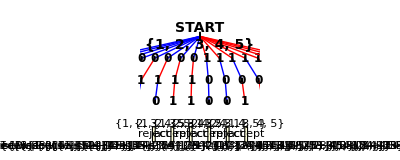

Decision tree for second state:

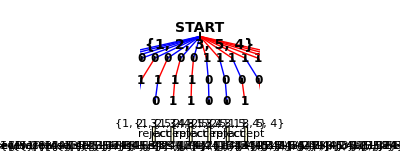

```mathematica
ClearAll["Global`*"]

(* =========================================*)
(*SETUP*)
(* =========================================*)

L=5;
nParticles=5;
β=Symbol["β"];

Print["L = ",L];
Print["nParticles = ",nParticles];

(* =========================================*)
(*SYMBOLIC J MATRIX*)
(* =========================================*)

GenerateSymbolicJ[n_]:=Module[{J=Table[0,{n+1},{n+1}]},Do[If[i<j,J[[i+1,j+1]]=Symbol["J"<>ToString[i]<>ToString[j]];
J[[j+1,i+1]]=J[[i+1,j+1]]],{i,0,n},{j,0,n}];
J]

JMatrix=GenerateSymbolicJ[nParticles];

Print["J Matrix:"];
Print[JMatrix//MatrixForm];

(* =========================================*)
(*ENERGY*)
(* =========================================*)

SymbolicEnergy[lattice_]:=Module[{E=0,i,j},Do[j=If[i==Length[lattice],1,i+1];
If[lattice[[i]]!=0&&lattice[[j]]!=0,E-=JMatrix[[lattice[[i]]+1,lattice[[j]]+1]]],{i,Length[lattice]}];
E]

(* =========================================*)
(*CONFIGURATIONS*)
(* =========================================*)

GenerateAllConfigs[L_,n_]:=Flatten[Table[Module[{lat=ConstantArray[0,L]},Do[lat[[pos[[i]]]]=perm[[i]],{i,n}];
lat],{pos,Subsets[Range[L],{n}]},{perm,Permutations[Range[n]]}],1]

states=GenerateAllConfigs[L,nParticles];
Print["Total configurations: ",Length[states]];
Print["First few: ",Take[states,Min[5,Length[states]]]];

(* =========================================*)
(*TREE RANDOMNESS*)
(* =========================================*)

$BinaryChoices={};
$BinaryIndex=1;

BinaryBit[]:=Module[{b},b=$BinaryChoices[[$BinaryIndex]];
$BinaryIndex++;
b]

DecodeInteger[nBits_]:=FromDigits[Table[BinaryBit[],{nBits}],2]



(* =========================================*)
(*KAWASAKI MOVE—normalized probabilities*)
(* =========================================*)

KawasakiMoveFromBits[lattice_]:=Module[{Lsize,nBits,raw,i,j,new,ΔE,p,siteProb},Lsize=Length[lattice];
(*siteProb=1/Lsize*) (*previous, but isn't normalised, probably not a problem though*)
nBits=Ceiling[Log2[Lsize]];
siteProb=1/(2^nBits);  (*Probability of this specific bit pattern*)

raw=DecodeInteger[nBits];
i=1+Mod[raw,Lsize];
j=If[i==Lsize,1,i+1];
If[lattice[[i]]==lattice[[j]],Return[{"no-swap",lattice,siteProb}]];
new=lattice;
new[[{i,j}]]=lattice[[{j,i}]];
ΔE=SymbolicEnergy[new]-SymbolicEnergy[lattice];
p=Piecewise[{{1,ΔE<=0},{Exp[-β ΔE],ΔE>0}}];
{{"accept",new,siteProb*p},{"reject",lattice,siteProb*(1-p)}}]





(* =========================================*)
(*TREE ENUMERATION*)
(* =========================================*)

EnumerateTree[lattice_]:=Module[{nBitsForSite,allBits,results},nBitsForSite=Ceiling[Log2[Length[lattice]]];
allBits=Tuples[{0,1},nBitsForSite];
results=Flatten[Table[($BinaryChoices=bits;
$BinaryIndex=1;
With[{out=KawasakiMoveFromBits[lattice]},If[First[out]==="no-swap",{{bits,"no-swap",out[[2]],out[[3]]}},{{bits,"accept",out[[1,2]],out[[1,3]]},{bits,"reject",out[[2,2]],out[[2,3]]}}]]),{bits,allBits}],1];
results]

(* =========================================*)
(*TREE VISUALIZATION—BIG,SCROLLABLE*)
(* =========================================*)

VisualizeDecisionTree[initialState_]:=Module[{tree,nBitsForSite,nBitsTotal,yLevels,xSpacing,nodeRadius,rootX,rootY,pathGraphics,baseXPositions,imageWidth,plotRangeX,Lsize,rootGraphics},tree=EnumerateTree[initialState];
Lsize=Length[initialState];
nBitsForSite=Ceiling[Log2[Lsize]];
nBitsTotal=nBitsForSite;
(*Use a wide layout for scrolling*)imageWidth=Max[1800,Length[tree]*60];
plotRangeX=Max[50,Length[tree]*3];
yLevels=Range[nBitsTotal,0,-1]*2;
xSpacing=Max[20,Length[tree]*1.5];
nodeRadius=0.2;
rootX=0;
rootY=yLevels[[1]];
baseXPositions=Table[(i-(Length[tree]+1)/2)*(xSpacing/1.5),{i,Length[tree]}];
pathGraphics=Table[Module[{path,pathType,finalState,probability,currentX,currentY,lineGraphics,circleGraphics,labelGraphics,bit,level,nextX,nextY,edgeColor,leafY,leafX,leafColor,leafText,treeEntry},treeEntry=tree[[i]];
path=Part[treeEntry,1];
pathType=Part[treeEntry,2];
finalState=Part[treeEntry,3];
probability=Part[treeEntry,4];
currentX=rootX;
currentY=rootY;
lineGraphics={};
circleGraphics={};
labelGraphics={};
Do[bit=path[[level]];
nextX=baseXPositions[[i]]+(currentX-baseXPositions[[i]])*0.3;
nextY=yLevels[[level+1]];
edgeColor=Which[bit==0,Blue,bit==1,Red,True,Black];
AppendTo[lineGraphics,{edgeColor,Thickness[0.0025],Arrowheads[0],Arrow[{{currentX,currentY},{nextX,nextY}}]}];
AppendTo[circleGraphics,{White,EdgeForm[{Black,Thin}],Disk[{nextX,nextY},nodeRadius]}];
AppendTo[labelGraphics,Text[Style[bit,Bold,12],{nextX,nextY}]];
currentX=nextX;
currentY=nextY;,{level,Length[path]}];
leafY=-3;
leafX=baseXPositions[[i]];
{leafColor,leafText}=Which[pathType=="no-swap",{LightGray,Column[{Style[ToString[finalState],Gray,12],Style["no-swap",Gray,10]},Center,Spacings->0.1]},pathType=="accept",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["accept",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]},pathType=="reject",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["reject",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]}];
AppendTo[circleGraphics,{leafColor,EdgeForm[{Black,Thin}],Rectangle[{leafX-1.2,leafY-0.7},{leafX+1.2,leafY+0.7}]}];
AppendTo[labelGraphics,Text[leafText,{leafX,leafY}]];
{lineGraphics,circleGraphics,labelGraphics}],{i,Length[tree]}];
rootGraphics={{LightBlue,EdgeForm[{Black,Thick}],Disk[{rootX,rootY},nodeRadius*2]},Text[Style["START\n"<>ToString[initialState],Bold,14],{rootX,rootY}]};
(*Wrap the tree in a scrollable pane*)Pane[Graphics[{pathGraphics,rootGraphics},PlotRange->{{-plotRangeX,plotRangeX},{-4,yLevels[[1]]+2}},AspectRatio->0.4,Background->White],{1800,600},Scrollbars->True]]

(* =========================================*)
(*TRANSITION MATRIX*)
(* =========================================*)

EnumerateTransitions[lattice_]:=Module[{tree},tree=EnumerateTree[lattice];
Merge[Table[{lattice,tree[[i,3]]}->tree[[i,4]],{i,Length[tree]}],Total]]

BuildTransitionMatrixold[states_]:=Module[{n,idx,M,trans},n=Length[states];
idx=AssociationThread[states->Range[n]];
M=ConstantArray[0,{n,n}];
Do[trans=EnumerateTransitions[s];
KeyValueMap[(M[[idx[#1[[1]]],idx[#1[[2]]]]]=Simplify[#2])&,trans],{s,states}];
M]


BuildTransitionMatrix[states_]:=Module[{n,idx,M,trans},n=Length[states];
idx=AssociationThread[states->Range[n]];
M=ConstantArray[0,{n,n}];
Do[trans=EnumerateTransitions[s];
KeyValueMap[(M[[idx[#1[[1]]],idx[#1[[2]]]]]=#2)&,(*NO Simplify*)trans],{s,states}];
M]

transitionMatrix=BuildTransitionMatrix[states];

Print["\nTransition matrix row sums: ",Simplify[Total[transitionMatrix,{2}]]];
Print["Transition matrix:"];
If[Length[states]<=10,Print[transitionMatrix//MatrixForm],Print["Showing 5x5 block:"];
Print[Take[transitionMatrix,{1,5},{1,5}]//MatrixForm]];





(* =========================================*)(*DETAILED BALANCE CHECK-OPTIMIZED*)(* =========================================*)(*Precompute unnormalized Boltzmann weights (Z cancels out)*)boltzmannWeights=Table[Exp[-β*SymbolicEnergy[states[[i]]]],{i,Length[states]}];

Print["Computing detailed balance violations..."];

(*Compute violations without Z factor*)
violations=Flatten[Table[boltzmannWeights[[i]]*transitionMatrix[[i,j]]-boltzmannWeights[[j]]*transitionMatrix[[j,i]],{i,Length[states]},{j,i+1,Length[states]}]];

(*Remove literal zeros*)
nonZero=DeleteCases[violations,0];

Print["Non-literal-zero violations: ",Length[nonZero]];

(*Remove duplicates before simplifying*)
uniqueViolations=DeleteDuplicates[nonZero];

Print["Unique violations to simplify: ",Length[uniqueViolations]," (reduced from ",Length[nonZero],")"];

(*Simplify only unique violations*)
If[Length[uniqueViolations]>0,Print["Applying FullSimplify to unique violations..."];
simplifiedUnique=ParallelMap[FullSimplify,uniqueViolations];
(*Count remaining violations*)remainingViolations=Select[simplifiedUnique,#=!=0&];
Print["\nDetailed balance: ",If[Length[remainingViolations]==0,"SATISFIED (all unique violations symbolically reduced to 0)",ToString[Length[remainingViolations]]<>" unique violations remain after FullSimplify"]];
(*Show remaining violations if small enough*)If[Length[remainingViolations]>0&&Length[remainingViolations]<=3,Print["Remaining violations: "];
Do[Print[remainingViolations[[i]]],{i,Length[remainingViolations]}]];,Print["\nDetailed balance: SATISFIED (all violations are literal zeros)"];];



(*

OLD DB CHECK which is slower

(* =========================================*)(*DETAILED BALANCE CHECK—fixed FullSimplify logic*)(* =========================================*)theoreticalDist=Table[Exp[-β*SymbolicEnergy[states[[i]]]],{i,Length[states]}];
Z=Total[theoreticalDist];
theoreticalDist=theoreticalDist/Z;

violations=Flatten[Table[theoreticalDist[[i]]*transitionMatrix[[i,j]]-theoreticalDist[[j]]*transitionMatrix[[j,i]],{i,Length[states]},{j,i+1,Length[states]}]];

(*Remove literal zeros*)
nonZero=DeleteCases[violations,0];

(*Attempt simplification if necessary*)If[Length[nonZero]>0,Module[{fsTest},fsTest=Quiet[Check[FullSimplify[nonZero[[1]]],"FAIL"]];
(*Use symbolic comparison to 0*)If[fsTest=!="FAIL"&&fsTest===0,(*FullSimplify all violations in parallel*)nonZero=ParallelMap[FullSimplify,nonZero];]]];

Print["\nDetailed balance: ",If[Length[Select[nonZero,#=!=0&]]==0,"SATISFIED",ToString[Length[Select[nonZero,#=!=0&]]]<>" violations"]];

(*   OLD CODE, USES A NUMERICAL TEST
(*Attempt simplification if necessary*)
If[Length[nonZero]>0,Module[{fsTest},fsTest=Quiet[Check[FullSimplify[nonZero[[1]]],"FAIL"]];
(*Use PossibleZeroQ instead of===0*)If[fsTest=!="FAIL"&&PossibleZeroQ[fsTest],(*FullSimplify all violations in parallel*)nonZero=ParallelMap[FullSimplify,nonZero];]]];

Print["\nDetailed balance: ",If[Length[Select[nonZero,!PossibleZeroQ[#]&]]==0,"SATISFIED",ToString[Length[Select[nonZero,!PossibleZeroQ[#]&]]]<>" violations"]];*)*)


(* =========================================*)
(*VISUALIZE TREES FOR FIRST TWO STATES*)
(* =========================================*)

Print["\nDecision tree for first state:"];
tree1=VisualizeDecisionTree[states[[1]]];
Print[tree1];

If[Length[states]>1,Print["\nDecision tree for second state:"];
tree2=VisualizeDecisionTree[states[[2]]];
Print[tree2];];
```

```mathematica
(* =========================================*)(*NUMERICAL SIMULATION*)(* =========================================*)(*Generate random symmetric J matrix*)GenerateRandomJMatrix[n_]:=Module[{J},J=Table[0,{n+1},{n+1}];
Do[If[i<j,J[[i+1,j+1]]=RandomReal[{-1,1}];
J[[j+1,i+1]]=J[[i+1,j+1]]],{i,0,n},{j,0,n}];
J]

(*Set numerical values*)
SeedRandom[1]; (*for reproducibility of J matrix*)
JMatrixNum=GenerateRandomJMatrix[nParticles];
βNum=1.0;

Print["Numerical J Matrix:"];
Print[JMatrixNum//MatrixForm];

(*Define numerical energy function*)
NumericalEnergy[lattice_]:=Module[{E=0,i,j},Do[j=If[i==Length[lattice],1,i+1];
If[lattice[[i]]!=0&&lattice[[j]]!=0,E-=JMatrixNum[[lattice[[i]]+1,lattice[[j]]+1]]],{i,Length[lattice]}];
E]

(*Replace symbolic J and β with numerical values for MCMC*)
JMatrix=JMatrixNum;
β=βNum;

(*Initial state*)
currentState=states[[1]];

(*Number of iterations*)
nSteps=500000;

(*Run simulation*)
SeedRandom[12];
trajectory=NestList[Function[lattice,Module[{nBits,bits,result},nBits=Ceiling[Log2[Length[lattice]]];
bits=RandomInteger[{0,1},nBits];
$BinaryChoices=bits;
$BinaryIndex=1;
result=KawasakiMoveFromBits[lattice];
If[First[result]==="no-swap",result[[2]],If[RandomReal[]<result[[1,3]],result[[1,2]],result[[2,2]]]]]],currentState,nSteps];

(*Print first few states*)
Print["First 10 states:"];
Print[Take[trajectory,10]];

(*Count state frequencies*)
stateCounts=Counts[trajectory];
Print["\nState frequencies:"];
Print[stateCounts//Normal];
```

Numerical J Matrix:

(0 | 0.634779 | -0.777161 | 0.579052 | -0.624394 | -0.517278
0.634779 | 0 | -0.868522 | 0.0844932 | -0.537691 | -0.207988
-0.777161 | -0.868522 | 0 | 0.400948 | -0.576348 | 0.497314
0.579052 | 0.0844932 | 0.400948 | 0 | -0.154299 | -0.50501
-0.624394 | -0.537691 | -0.576348 | -0.154299 | 0 | 0.954344
-0.517278 | -0.207988 | 0.497314 | -0.50501 | 0.954344 | 0)

First 10 states:

{{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,4,5},{1,2,3,5,4},{1,2,3,5,4},{1,2,3,5,4},{1,2,3,5,4},{1,2,3,5,4}}

State frequencies:

{{1,2,3,4,5}→4541,{1,2,3,5,4}→2766,{2,1,3,5,4}→1752,{2,1,3,4,5}→6948,{2,3,1,4,5}→14035,{1,3,2,4,5}→8085,{1,3,4,2,5}→3407,{1,3,4,5,2}→6762,{3,1,4,5,2}→15528,{2,3,4,5,1}→3991,{2,3,5,4,1}→2145,{3,2,5,4,1}→16242,{3,5,2,4,1}→1378,{3,5,4,2,1}→1482,{5,3,2,4,1}→1132,{3,2,4,5,1}→7475,{3,2,5,1,4}→4704,{2,3,5,1,4}→1119,{2,5,3,1,4}→1399,{5,2,3,1,4}→17898,{2,5,1,3,4}→3317,{4,5,3,1,2}→1660,{4,3,5,1,2}→284,{3,4,5,1,2}→4402,{3,4,5,2,1}→7248,{1,4,5,2,3}→16759,{1,5,4,2,3}→8697,{3,4,2,5,1}→2590,{1,4,2,5,3}→1445,{5,3,2,1,4}→2378,{5,2,1,3,4}→7645,{4,2,1,3,5}→1489,{4,2,3,1,5}→7385,{4,3,2,1,5}→4763,{4,3,1,2,5}→6131,{4,3,2,5,1}→4235,{4,1,5,2,3}→3854,{4,1,2,5,3}→653,{4,1,2,3,5}→2100,{4,1,3,2,5}→14835,{2,4,3,1,5}→2598,{2,4,3,5,1}→503,{3,1,5,4,2}→7659,{3,5,1,4,2}→1163,{2,5,1,4,3}→4211,{2,5,4,1,3}→16586,{3,5,4,1,2}→2262,{2,4,5,1,3}→7398,{2,5,4,3,1}→6819,{5,2,4,3,1}→2460,{5,4,2,3,1}→8397,{5,4,3,2,1}→4400,{4,5,2,3,1}→16017,{5,4,2,1,3}→1529,{4,5,2,1,3}→6093,{5,2,4,1,3}→1504,{3,4,2,1,5}→422,{5,1,2,3,4}→4692,{5,1,3,2,4}→8489,{1,4,3,2,5}→4053,{1,3,2,5,4}→17237,{3,1,2,4,5}→1560,{3,1,2,5,4}→6957,{4,3,5,2,1}→935,{5,2,3,4,1}→3972,{2,5,3,4,1}→656,{1,5,3,4,2}→342,{5,1,3,4,2}→3065,{5,1,4,3,2}→4089,{4,5,1,3,2}→8341,{5,4,1,3,2}→17339,{5,4,3,1,2}→6305,{1,3,5,2,4}→1773,{1,5,3,2,4}→1043,{1,5,2,4,3}→3210,{4,5,1,2,3}→4136,{5,4,1,2,3}→2472,{3,4,1,2,5}→759,{5,1,4,2,3}→1046,{5,1,2,4,3}→494,{1,2,4,5,3}→1773,{2,1,4,5,3}→2629,{1,2,5,4,3}→7311,{3,5,2,1,4}→769,{1,2,5,3,4}→642,{2,3,4,1,5}→3185,{2,3,1,5,4}→7052,{4,3,1,5,2}→2997,{3,4,1,5,2}→3827,{2,4,5,3,1}→1836,{3,2,1,5,4}→4539,{3,1,5,2,4}→3043,{1,3,5,4,2}→1383,{4,5,3,2,1}→2294,{4,1,5,3,2}→940,{2,1,5,3,4}→387,{2,1,5,4,3}→4507,{5,3,4,2,1}→502,{1,5,2,3,4}→3744,{5,3,1,4,2}→1674,{4,2,3,5,1}→1439,{1,5,4,3,2}→4341,{1,4,5,3,2}→2672,{2,4,1,5,3}→919,{5,3,4,1,2}→798,{3,2,1,4,5}→2023,{3,2,4,1,5}→633,{2,4,1,3,5}→1310,{4,1,3,5,2}→1399,{2,1,4,3,5}→903,{4,2,5,3,1}→1591,{4,2,5,1,3}→2493,{5,2,1,4,3}→1109,{5,3,1,2,4}→1500,{3,5,1,2,4}→343,{1,4,2,3,5}→879,{1,2,4,3,5}→411,{3,1,4,2,5}→1393,{1,4,3,5,2}→900,{4,2,1,5,3}→266}

Observed counts: {4541,2766,411,1773,642,7311,8085,17237,3407,6762,1773,1383,879,1445,4053,900,16759,2672,3744,3210,1043,342,8697,4341,6948,1752,903,2629,387,4507,14035,7052,3185,3991,1119,2145,1310,919,2598,503,7398,1836,3317,4211,1399,656,16586,6819,1560,6957,1393,15528,3043,7659,2023,4539,633,7475,4704,16242,759,3827,422,2590,4402,7248,343,1163,769,1378,2262,1482,2100,653,14835,1399,3854,940,1489,266,7385,1439,2493,1591,6131,2997,4763,4235,284,935,4136,8341,6093,16017,1660,2294,4692,494,8489,3065,1046,4089,7645,1109,17898,3972,1504,2460,1500,1674,2378,1132,798,502,2472,17339,1529,8397,6305,4400}

Total observations: 500001

============================================================

CORRELATION ANALYSIS

============================================================

Pearson correlation coefficient: 0.9947

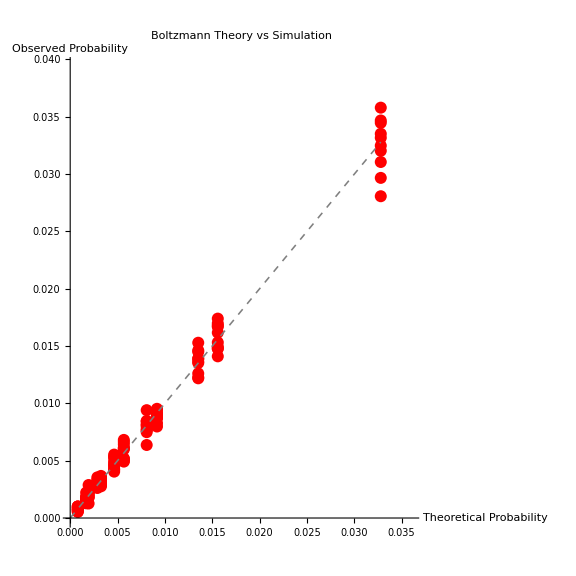

```mathematica
(* =========================================*)(*BOLTZMANN DISTRIBUTION ANALYSIS*)(* =========================================*)(*Step 1:Calculate energy for each state*)

energies=Table[NumericalEnergy[states[[i]]],{i,Length[states]}];

(*Step 2& 3:Calculate Boltzmann distribution*)boltzmannWeights=Exp[-βNum*energies];
partitionFunction=Total[boltzmannWeights];
theoreticalProbs=boltzmannWeights/partitionFunction;

(*Step 4:Get observed probabilities from simulation-FIXED*)observedCounts=Table[If[KeyExistsQ[stateCounts,states[[i]]],stateCounts[states[[i]]],0],{i,Length[states]}];

Print["Observed counts: ",observedCounts];
Print["Total observations: ",Total[observedCounts]];

(*Only calculate probabilities if we have observations*)
If[Total[observedCounts]>0,observedProbs=N[observedCounts/Total[observedCounts]],Print["ERROR: No observations found!"];
observedProbs=Table[0,{Length[states]}];];

(*Scatter plot:theory vs observed*)scatterPlot=ListPlot[Table[{theoreticalProbs[[i]],observedProbs[[i]]},{i,Length[states]}],PlotStyle->{Red,PointSize[0.015]},PlotLabel->"Boltzmann Theory vs Simulation",AxesLabel->{"Theoretical Probability","Observed Probability"},AspectRatio->1,Epilog->{Dashed,Gray,Thickness[0.002],Line[{{0,0},{Max[theoreticalProbs],Max[theoreticalProbs]}}]},ImageSize->Large,PlotRange->{{0,Max[theoreticalProbs]*1.1},{0,Max[observedProbs]*1.1}}];

(*Calculate correlation coefficient*)
correlation=Correlation[theoreticalProbs,observedProbs];

Print["\n"<>StringRepeat["=",60]];
Print["CORRELATION ANALYSIS"];
Print[StringRepeat["=",60]];
Print["Pearson correlation coefficient: ",NumberForm[correlation,{5,4}]];
Print["\n"];
Print[scatterPlot];
```